find a fit to describe intra- to extra-cavity waist for a 6.35 mm thick substrate 5 mm RoC mirror with spherical back. data points from Zemax models.

{A→1273.41,a→0.238894,b→146.268}

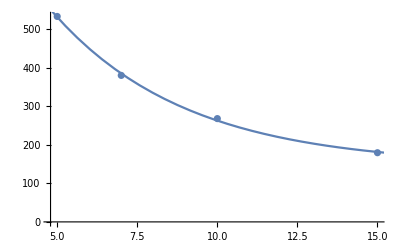

```mathematica
wcav={5,7,10,15};(*um*)
w2={533.6,380.5,268.3,179.7};(*um*)
data=Transpose@@{{wcav,w2}};
model=A Exp[-a x] +b;
fit=FindFit[data,model,{A,a,b},x]
Show[ListPlot[data],
Plot[model/.fit,{x,1,20}]]
```

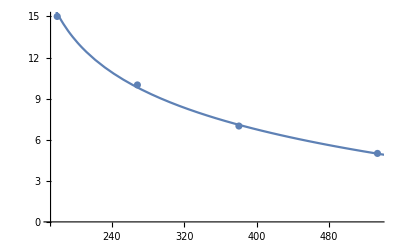

```mathematica
modelInverse=-1/a Log[(x-b)/A];
Show[ListPlot[Transpose@@{{w2,wcav}}],
Plot[modelInverse/.fit,{x,100,600}]]
```

```mathematica
trend=modelInverse/.fit
trend/.x->0.194//N
```

-4.18595 Log[0.000785291 (-146.268+x)]

9.06403-13.1506 ⅈ

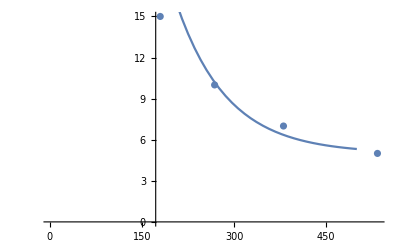

```mathematica
wcav={5,7,10,15};(*um*)
w2={533.6,380.5,268.3,179.7};(*um*)
data=Transpose@@{{w2,wcav}};
model=A Exp[-a (x-xx)]+b;
(*fit=FindFit[data,model,{A,a,b,xx},x]*)
Show[ListPlot[data],
Plot[model/.{A->15,a->0.012,b->5,xx->180},{x,1,500}],PlotRange->{0,15}]
```

```mathematica
trend=model/.fit;
trend/.x->13.5
```

193.226

```mathematica
model
```

b+A ⅇ^(-a x^2)